```mathematica
R = d(h/K+a/(a-2) )+ Exp[-2 h(1/2 - b/h)^2]*2a Log[n]/d
```

d (a/(-2+a)+h/K)+(2 a ⅇ^(-2 (1/2-b/h)^2 h) Log[n])/d

```mathematica
D[R,h]
```

d/K+(2 a ⅇ^(-2 (1/2-b/h)^2 h) (-2 (1/2-b/h)^2-(4 b (1/2-b/h))/h) Log[n])/d

```mathematica
(2 a ⅇ^(-2 (1/2-b/h)^2 h) (-2 (1/2-b/h)^2-(4 b (1/2-b/h))/h) Log[n])/d//.{ b-> 50, a-> 4,}
```

(8 ⅇ^(-2 (1/2-50/h)^2 h) (-2 (1/2-50/h)^2-(200 (1/2-50/h))/h) Log[n])/d

```mathematica
R = h*d/2+ (n-h)*(2Exp[-h/2]+Exp[-h*d^2/8]+Exp[-3h*d^2/8])
```

```mathematica
(d h)/2+(2 ⅇ^(-h/2)+ⅇ^(-(3 d^2 h)/8)+ⅇ^(-(d^2 h)/8)) (-h+n)

(d h)/2+(2 ⅇ^(-h/2)+ⅇ^(-(3 d^2 h)/8)+ⅇ^(-(d^2 h)/8)) (-h+n) //. {n -> 100,d->0.1}
```

```mathematica
h->(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/d^2
(d h)/2+Min[(2 ⅇ^(-h/2)+ⅇ^(-(3 d^2 h)/8)+ⅇ^(-(d^2 h)/8)),1/2]* (-h+n)*d /. h->(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/d^2
```

h→(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/d^2

d Min[1/2,ⅇ^(-3/8 (8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)]))+2 ⅇ^(-(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/(2 d^2))+ⅇ^(1/8 (-8-d^2 n+8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)]))] (n-(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/d^2)+(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/(2 d)

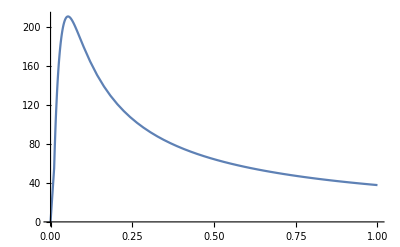

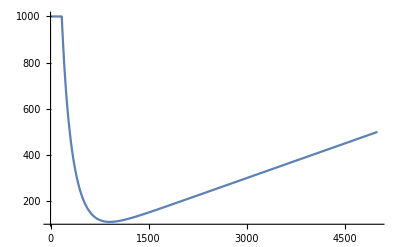

```mathematica
Plot[(d h)/2+Min[(2 ⅇ^(-h/2)+ⅇ^(-(3 d^2 h)/8)+ⅇ^(-(d^2 h)/8)),1/2]* (-h+n)*d //. {n -> 10000,h->(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/d^2},{d,0,1}]

Plot[(d h)/2+Min[(2 ⅇ^(-h/2)+ⅇ^(-(3 d^2 h)/8)+ⅇ^(-(d^2 h)/8)),1/2]* (-h+n)*d //. {n -> 10000,d->0.2},{h,0,5000}]
```

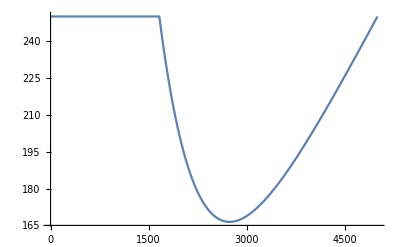

```mathematica
Plot[(d h)/2+Min[(4 ⅇ^(-(d^2 h)/8)),1/2]* (-h+n)*d //. {n -> 5000,d->0.1},{h,0,5000}]
```

```mathematica
R = (d h)/2+(4 ⅇ^(-(d^2 h)/8))* (-h+n)*d
```

(d h)/2+4 d ⅇ^(-(d^2 h)/8) (-h+n)

```mathematica
Solve[D[R,h]==0,h]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{h->(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/d^2}}
(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/d^2 //. {n -> 5000,d->0.2}
```

{{h→(8+d^2 n-8 ProductLog[1/8 ⅇ^(1+(d^2 n)/8)])/d^2}}

1023.66

```mathematica
D[R,h]
```

d/2-d (2 ⅇ^(-h/2)+ⅇ^(-(3 d^2 h)/8)+ⅇ^(-(d^2 h)/8))+d (-ⅇ^(-h/2)-3/8 d^2 ⅇ^(-(3 d^2 h)/8)-1/8 d^2 ⅇ^(-(d^2 h)/8)) (-h+n)

```mathematica
Solve[D[R,h]==0,h]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[d/2-d (2 ⅇ^(-h/2)+ⅇ^(-(3 d^2 h)/8)+ⅇ^(-(d^2 h)/8))+d (-ⅇ^(-h/2)-3/8 d^2 ⅇ^(-(3 d^2 h)/8)-1/8 d^2 ⅇ^(-(d^2 h)/8)) (-h+n)==0,h]

```mathematica
Solve[d/2-2 ⅇ^(-h/2)-ⅇ^(-(3 d^2 h)/8)-ⅇ^(-(d^2 h)/8)+(-ⅇ^(-h/2)-3/8 d^2 ⅇ^(-(3 d^2 h)/8)-1/8 d^2 ⅇ^(-(d^2 h)/8)) (-h+n)==0,h]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[d/2-2 ⅇ^(-h/2)-ⅇ^(-(3 d^2 h)/8)-ⅇ^(-(d^2 h)/8)+(-ⅇ^(-h/2)-3/8 d^2 ⅇ^(-(3 d^2 h)/8)-1/8 d^2 ⅇ^(-(d^2 h)/8)) (-h+n)==0,h]

```mathematica
Exp[0]
```

1

```mathematica
R = h*d/2+2*(n-h)*(Exp[-h/2]+Exp[-h/2*(d/2)^2])
```

(d h)/2+2 (ⅇ^(-h/2)+ⅇ^(-(d^2 h)/8)) (-h+n)

```mathematica
D[R,h]
```

```mathematica
d/2-2 (ⅇ^(-h/2)+ⅇ^(-(d^2 h)/8))+2 (-1/2 ⅇ^(-h/2)-1/8 d^2 ⅇ^(-(d^2 h)/8)) (-h+n)

S = Series[d/2-2 (ⅇ^(-h/2)+ⅇ^(-(d^2 h)/8))+2 (-1/2 ⅇ^(-h/2)-1/8 d^2 ⅇ^(-(d^2 h)/8)) (-h+n),{h,n/2,1}]
```

d/2-2 (ⅇ^(-h/2)+ⅇ^(-(d^2 h)/8))+2 (-1/2 ⅇ^(-h/2)-1/8 d^2 ⅇ^(-(d^2 h)/8)) (-h+n)

```mathematica
(d/2-2 ⅇ^(-n/4)-2 ⅇ^(-(d^2 n)/16)-1/2 ⅇ^(-n/4) n-1/8 d^2 ⅇ^(-(d^2 n)/16) n)+(2 ⅇ^(-n/4)+1/2 d^2 ⅇ^(-(d^2 n)/16)+1/4 ⅇ^(-n/4) n+1/64 d^4 ⅇ^(-(d^2 n)/16) n) (h-n/2)+O[h-n/2]^2
Solve[(d/2-2 ⅇ^(-n/4)-2 ⅇ^(-(d^2 n)/16)-1/2 ⅇ^(-n/4) n-1/8 d^2 ⅇ^(-(d^2 n)/16) n)+(2 ⅇ^(-n/4)+1/2 d^2 ⅇ^(-(d^2 n)/16)+1/4 ⅇ^(-n/4) n+1/64 d^4 ⅇ^(-(d^2 n)/16) n) (h-n/2)==0,h]
```

(d/2-2 ⅇ^(-n/4)-2 ⅇ^(-(d^2 n)/16)-1/2 ⅇ^(-n/4) n-1/8 d^2 ⅇ^(-(d^2 n)/16) n)+(2 ⅇ^(-n/4)+1/2 d^2 ⅇ^(-(d^2 n)/16)+1/4 ⅇ^(-n/4) n+1/64 d^4 ⅇ^(-(d^2 n)/16) n) (h-n/2)+O[h-n/2]^2

```mathematica
{{h->(256 ⅇ^(n/4)+256 ⅇ^((d^2 n)/16)-64 d ⅇ^(n/4+(d^2 n)/16)+48 d^2 ⅇ^(n/4) n+192 ⅇ^((d^2 n)/16) n+d^4 ⅇ^(n/4) n^2+16 ⅇ^((d^2 n)/16) n^2)/(2 (32 d^2 ⅇ^(n/4)+128 ⅇ^((d^2 n)/16)+d^4 ⅇ^(n/4) n+16 ⅇ^((d^2 n)/16) n))}}
(256 ⅇ^(n/4)+256 ⅇ^((d^2 n)/16)-64 d ⅇ^(n/4+(d^2 n)/16)+48 d^2 ⅇ^(n/4) n+192 ⅇ^((d^2 n)/16) n+d^4 ⅇ^(n/4) n^2+16 ⅇ^((d^2 n)/16) n^2)/(2 (32 d^2 ⅇ^(n/4)+128 ⅇ^((d^2 n)/16)+d^4 ⅇ^(n/4) n+16 ⅇ^((d^2 n)/16) n)) //.{d->0.2,n->100}
```

{{h→(256 ⅇ^(n/4)+256 ⅇ^((d^2 n)/16)-64 d ⅇ^(n/4+(d^2 n)/16)+48 d^2 ⅇ^(n/4) n+192 ⅇ^((d^2 n)/16) n+d^4 ⅇ^(n/4) n^2+16 ⅇ^((d^2 n)/16) n^2)/(2 (32 d^2 ⅇ^(n/4)+128 ⅇ^((d^2 n)/16)+d^4 ⅇ^(n/4) n+16 ⅇ^((d^2 n)/16) n))}}

155.404

```mathematica
(d/2-2 ⅇ^(-n/4)-2 ⅇ^(-(d^2 n)/16)-1/2 ⅇ^(-n/4) n-1/8 d^2 ⅇ^(-(d^2 n)/16) n)+(2 ⅇ^(-n/4)+1/2 d^2 ⅇ^(-(d^2 n)/16)+1/4 ⅇ^(-n/4) n+1/64 d^4 ⅇ^(-(d^2 n)/16) n) (h-n/2)+(-3/4 ⅇ^(-n/4)-3/64 d^4 ⅇ^(-(d^2 n)/16)-1/16 ⅇ^(-n/4) n-(d^6 ⅇ^(-(d^2 n)/16) n)/1024) (h-n/2)^2+O[h-n/2]^3
(d/2-2 ⅇ^(-n/4)-2 ⅇ^(-(d^2 n)/16)-1/2 ⅇ^(-n/4) n-1/8 d^2 ⅇ^(-(d^2 n)/16) n)+(2 ⅇ^(-n/4)+1/2 d^2 ⅇ^(-(d^2 n)/16)+1/4 ⅇ^(-n/4) n+1/64 d^4 ⅇ^(-(d^2 n)/16) n) (h-n/2)+(-3/4 ⅇ^(-n/4)-3/64 d^4 ⅇ^(-(d^2 n)/16)-1/16 ⅇ^(-n/4) n-(d^6 ⅇ^(-(d^2 n)/16) n)/1024) (h-n/2)^2+O[h-n/2]^3
```

(d/2-2 ⅇ^(-n/4)-2 ⅇ^(-(d^2 n)/16)-1/2 ⅇ^(-n/4) n-1/8 d^2 ⅇ^(-(d^2 n)/16) n)+(2 ⅇ^(-n/4)+1/2 d^2 ⅇ^(-(d^2 n)/16)+1/4 ⅇ^(-n/4) n+1/64 d^4 ⅇ^(-(d^2 n)/16) n) (h-n/2)+(-3/4 ⅇ^(-n/4)-3/64 d^4 ⅇ^(-(d^2 n)/16)-1/16 ⅇ^(-n/4) n-(d^6 ⅇ^(-(d^2 n)/16) n)/1024) (h-n/2)^2+O[h-n/2]^3

(d/2-2 ⅇ^(-n/4)-2 ⅇ^(-(d^2 n)/16)-1/2 ⅇ^(-n/4) n-1/8 d^2 ⅇ^(-(d^2 n)/16) n)+(2 ⅇ^(-n/4)+1/2 d^2 ⅇ^(-(d^2 n)/16)+1/4 ⅇ^(-n/4) n+1/64 d^4 ⅇ^(-(d^2 n)/16) n) (h-n/2)+(-3/4 ⅇ^(-n/4)-3/64 d^4 ⅇ^(-(d^2 n)/16)-1/16 ⅇ^(-n/4) n-(d^6 ⅇ^(-(d^2 n)/16) n)/1024) (h-n/2)^2+O[h-n/2]^3

```mathematica
Solve[(d/2-2 ⅇ^(-n/4)-2 ⅇ^(-(d^2 n)/16)-1/2 ⅇ^(-n/4) n-1/8 d^2 ⅇ^(-(d^2 n)/16) n)+(2 ⅇ^(-n/4)+1/2 d^2 ⅇ^(-(d^2 n)/16)+1/4 ⅇ^(-n/4) n+1/64 d^4 ⅇ^(-(d^2 n)/16) n) (h-n/2)+(-3/4 ⅇ^(-n/4)-3/64 d^4 ⅇ^(-(d^2 n)/16)-1/16 ⅇ^(-n/4) n-(d^6 ⅇ^(-(d^2 n)/16) n)/1024) (h-n/2)^2==0,h]
```

```mathematica
{{h->(-2048 d^2 ⅇ^(n/4)-8192 ⅇ^((d^2 n)/16)-256 d^4 ⅇ^(n/4) n-4096 ⅇ^((d^2 n)/16) n-4 d^6 ⅇ^(n/4) n^2-256 ⅇ^((d^2 n)/16) n^2-√((2048 d^2 ⅇ^(n/4)+8192 ⅇ^((d^2 n)/16)+256 d^4 ⅇ^(n/4) n+4096 ⅇ^((d^2 n)/16) n+4 d^6 ⅇ^(n/4) n^2+256 ⅇ^((d^2 n)/16) n^2)^2-4 (-192 d^4 ⅇ^(n/4)-3072 ⅇ^((d^2 n)/16)-4 d^6 ⅇ^(n/4) n-256 ⅇ^((d^2 n)/16) n) (-8192 ⅇ^(n/4)-8192 ⅇ^((d^2 n)/16)+2048 d ⅇ^(n/4+(d^2 n)/16)-1536 d^2 ⅇ^(n/4) n-6144 ⅇ^((d^2 n)/16) n-80 d^4 ⅇ^(n/4) n^2-1280 ⅇ^((d^2 n)/16) n^2-d^6 ⅇ^(n/4) n^3-64 ⅇ^((d^2 n)/16) n^3)))/(2 (-192 d^4 ⅇ^(n/4)-3072 ⅇ^((d^2 n)/16)-4 d^6 ⅇ^(n/4) n-256 ⅇ^((d^2 n)/16) n))},{h->(-2048 d^2 ⅇ^(n/4)-8192 ⅇ^((d^2 n)/16)-256 d^4 ⅇ^(n/4) n-4096 ⅇ^((d^2 n)/16) n-4 d^6 ⅇ^(n/4) n^2-256 ⅇ^((d^2 n)/16) n^2+√((2048 d^2 ⅇ^(n/4)+8192 ⅇ^((d^2 n)/16)+256 d^4 ⅇ^(n/4) n+4096 ⅇ^((d^2 n)/16) n+4 d^6 ⅇ^(n/4) n^2+256 ⅇ^((d^2 n)/16) n^2)^2-4 (-192 d^4 ⅇ^(n/4)-3072 ⅇ^((d^2 n)/16)-4 d^6 ⅇ^(n/4) n-256 ⅇ^((d^2 n)/16) n) (-8192 ⅇ^(n/4)-8192 ⅇ^((d^2 n)/16)+2048 d ⅇ^(n/4+(d^2 n)/16)-1536 d^2 ⅇ^(n/4) n-6144 ⅇ^((d^2 n)/16) n-80 d^4 ⅇ^(n/4) n^2-1280 ⅇ^((d^2 n)/16) n^2-d^6 ⅇ^(n/4) n^3-64 ⅇ^((d^2 n)/16) n^3)))/(2 (-192 d^4 ⅇ^(n/4)-3072 ⅇ^((d^2 n)/16)-4 d^6 ⅇ^(n/4) n-256 ⅇ^((d^2 n)/16) n))}} //.{d->0.2,n->1000}
```

{{h→663.636+123.581 ⅈ},{h→663.636-123.581 ⅈ}}

```mathematica
R = d*h/2+2(Exp[-h/2]+Exp[-h*d^2/8])*(n-h)*d
```

(d h)/2+2 d (ⅇ^(-h/2)+ⅇ^(-(d^2 h)/8)) (-h+n)

```mathematica
R
```

(d h)/2+2 d (ⅇ^(-h/2)+ⅇ^(-(d^2 h)/8)) (-h+n)

```mathematica
R /. h -> 8*Log[n]/d^2
```

(4 Log[n])/d+2 d (1/n+n^(-4/d^2)) (n-(8 Log[n])/d^2)

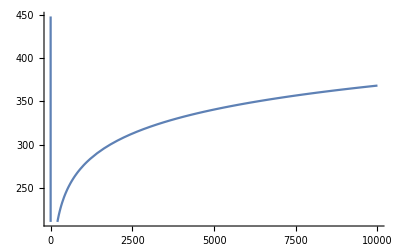

```mathematica
Plot[(4 Log[n])/d+2 d (1/n+n^(-4/d^2)) (n-(8 Log[n])/d^2)/.d->0.1,{n,0,10000}]
```

```mathematica
(4 Log[n])/d+2 d (1/n+n^(-4/d^2)) (n-(8 Log[n])/d^2) /. n->1000
```

(4 Log[1000])/d+2 (1/1000+1000^(-4/d^2)) d (1000-(8 Log[1000])/d^2)

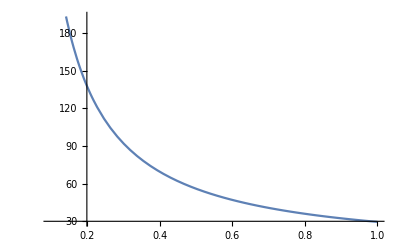

```mathematica
Plot[(4 Log[1000])/d+2 (1/1000+1000^(-4/d^2)) d (1000-(8 Log[1000])/d^2),{d,0.1,1}]
```

```mathematica
R = h*d/2+2(n-h)*d*Exp[-h*d^2/4]
```

(d h)/2+2 d ⅇ^(-(d^2 h)/4) (-h+n)

```mathematica
R /. h -> 4*Log[n]/d^2
```

(2 Log[n])/d+(2 d (n-(4 Log[n])/d^2))/n

```mathematica
D[R,h]
```

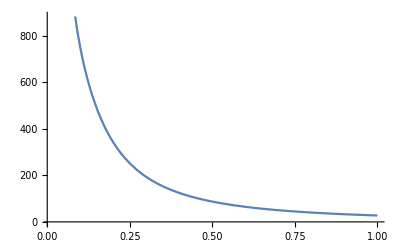

```mathematica
Plot[(4+d^2 n-4 ProductLog[1/4 ⅇ^(1+(d^2 n)/4)])/d^2//.{n->1000},{d,0.01,1}]
```

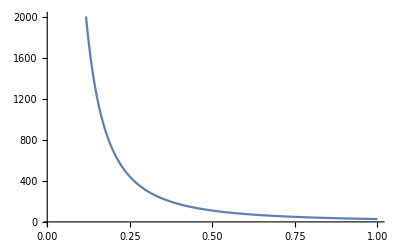

```mathematica
Plot[4*Log[n]/d^2 //.{n->1000},{d,0.01,1}]
```

```mathematica
Solve[D[x+x*Exp[x^2],x]==0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-√(1/2 (-1+2 ProductLog[-(√ⅇ)/2]))},{x→√(1/2 (-1+2 ProductLog[-(√ⅇ)/2]))}}

```mathematica
Solve[D[x*Exp[-c*x^2],x]==0,x]
```

{{x→-1/(√2 √c)},{x→1/(√2 √c)}}

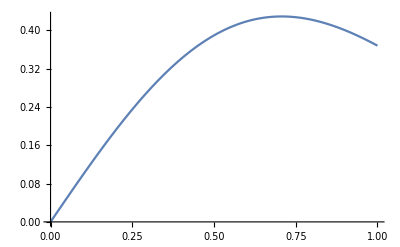

```mathematica
Plot[x*Exp[-x^2],{x,0,1}]
```

```mathematica
N[Exp[-1]]
```

0.367879

```mathematica
ClearAll["Global`*"]
```

```mathematica
R = h + T(Sqrt[8/h*Log[T*K/2]]+1/T)
```

h+T (1/T+2 √2 √(Log[(K T)/2]/h))

```mathematica
Solve[D[R,h]==0,h]
```

{{h→-(-2)^(1/3) T^(2/3) Log[(K T)/2]^(1/3)},{h→2^(1/3) T^(2/3) Log[(K T)/2]^(1/3)},{h→(-1)^(2/3) 2^(1/3) T^(2/3) Log[(K T)/2]^(1/3)}}

```mathematica
R = h + (T-h)(Sqrt[4/h * Log[h K/2]]+2/h)
```

h+(-h+T) (2/h+2 √(Log[(h K)/2]/h))

```mathematica
R /. h->T^(2/3) Log[(K T)/2]^(1/3)
```

```mathematica
FullSimplify[T (2 √(Log[(K T)/2]^(2/3)/T^(2/3))+2/(T^(2/3) Log[(K T)/2]^(1/3)))+T^(2/3) Log[(K T)/2]^(1/3)]
```

```mathematica
R =2 T √(Log[(K T)/2]^(2/3)/T^(2/3))+(2 T^(1/3))/Log[(K T)/2]^(1/3)+T^(2/3) Log[(K T)/2]^(1/3)
```

2 T √(Log[(K T)/2]^(2/3)/T^(2/3))+(2 T^(1/3))/Log[(K T)/2]^(1/3)+T^(2/3) Log[(K T)/2]^(1/3)

```mathematica
R /. K -> T^2
```

2 T √((Log[T^3/2]^(2/3))/T^(2/3))+(2 T^(1/3))/(Log[T^3/2]^(1/3))+T^(2/3) Log[T^3/2]^(1/3)

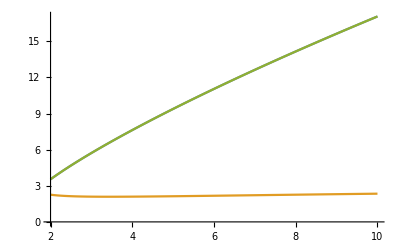

```mathematica
Plot[{2 T^(2/3) Log[T^3/2]^(1/3),(2 T^(1/3))/(Log[T^3/2]^(1/3)),2 T √((Log[T^3/2]^(2/3))/T^(2/3))},{T,2,10}]
```

```mathematica
2 - 2/3
```

```mathematica
4/3*1/2
```

2/3

```mathematica
T^(1/2)*T^(1/6)
```

T^(2/3)

```mathematica
N[2*Log[2]^(2/3)]
```

1.56644

```mathematica
2 T √(Log[(K T)/2]^(2/3)/T^(2/3))== 2 T √(Log[(K T)/2]^(2/3)/T^(2/3))
```

```mathematica
True
```

```mathematica
PowerExpand[2 T √(Log[(K T)/2]^(2/3)/T^(2/3))]
```

```mathematica
2 T^(2/3) (Log[(K T)/2])^(1/3) == 2 T √(Log[(K T)/2]^(2/3)/T^(2/3))
```

2 T^(2/3) Log[(K T)/2]^(1/3)==2 T √(Log[(K T)/2]^(2/3)/T^(2/3))

```mathematica
N[(T^2/3(Log[K T])^(1/3))/(T^1/3(Log[K T])^(-1/3))//.{T->2,K->2}]
```

2.48657

```mathematica
N[10000^(1/3)]
```

21.5443

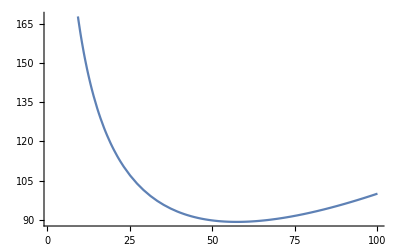

```mathematica
Plot[R //.{K -> 50, T-> 100},{h,1,100}]
```

```mathematica
So there is a nice minimum - why can't I get it analytically ... arg
```

```mathematica
DevR = D[R,h]
```

1-2/h-2 √(Log[(h K)/2]/h)+(-h+T) (-2/h^2+(1/h^2-Log[(h K)/2]/h^2)/(√(Log[(h K)/2]/h)))

```mathematica
Solve[DevR ==0, h]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1-2/h-2 √(Log[(h K)/2]/h)+(-h+T) (-2/h^2+(1/h^2-Log[(h K)/2]/h^2)/(√(Log[(h K)/2]/h)))==0,h]

```mathematica
Ok so lets try and pick something that is a simple function and returns something close to the minimum
```

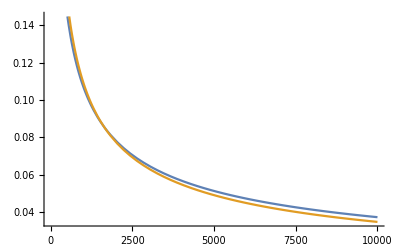

```mathematica
Plot[{Sqrt[1/x*Log[100*x]],Sqrt[12/x]},{x,1,10000}]
```

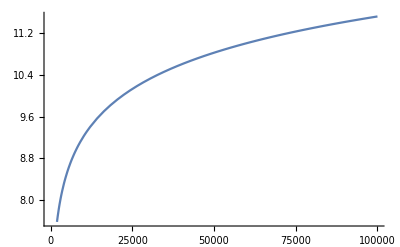

```mathematica
Plot[Log[x],{x,0,100000}]
```

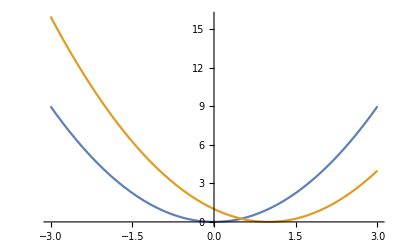

```mathematica
Plot[{x^2,(x-1)^2},{x,-3,3}]
```

```mathematica
PowerExpand[Log[n^2]]
```

2 Log[n]

```mathematica
R
```